```mathematica
FourierTransform[1/(√(2π))Exp[I (-ω0)*t],t,ω]
```

DiracDelta[ω-ω0]

```mathematica
FourierTransform[Exp[-t^2] Sin[t],t,ω]
```

(ⅈ (-1+Cosh[ω]+Sinh[ω]) (Cosh[1/4 (1+ω)^2]-Sinh[1/4 (1+ω)^2]))/(2 √2)

Ω^2/(2 Γ^2 (1+(2 Ω^2)/Γ^2))

(Ω^2 (1-(2 Ω^2)/Γ^2+(Γ (1-(10 Ω^2)/Γ^2))/(4 √(Γ^2/16-Ω^2))))/(4 Γ^2 (1+(2 Ω^2)/Γ^2)^2)

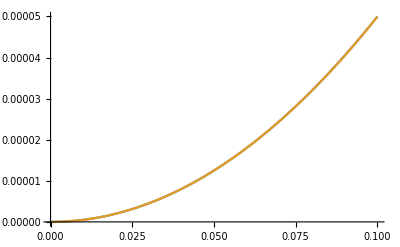

```mathematica
Y = (√2 Ω)/Γ;
δ= √((Γ/4)^2-Ω^2);

incoherentCorrelation1=1/4 Y^2/(1+Y^2)Exp[-(Γ/2)t]Exp[-I ω0 t];

(*incoherentCorrelation2 = 1/8 Y^2/((1+Y^2)^2)[1-Y^2+(1-5 Y^2)(Γ/4)/δ]Exp[-((3Γ/4)-δ)t];*)
(*FourierTransform[incoherentCorrelation2, t, ω]*)
ic1 = (
ComplexExpand[FourierTransform[ComplexExpand[incoherentCorrelation1], t, ω]]
);

central = 1/4 Y^2/(1+Y^2)
peak = 1/8 Y^2/((1+Y^2)^2)(1-Y^2+(1-5 Y^2)(Γ/4)/δ)
Plot[{
central/.Γ -> 10,
peak/.Γ -> 10
},{Ω,0,0.1}]
```

# Lorentzian plots

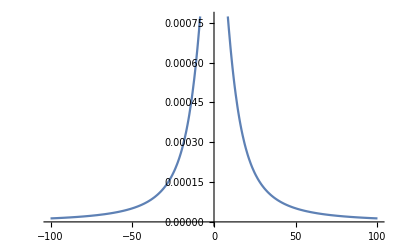

```mathematica
g = Γ/2;
central = 1/(2π)1/4 Y^2/(1+Y^2)g/(g^2+δω^2);

g = 
side = 1/8 Y^2/((1+Y^2)^2)(1-Y^2)
Plot[
central
/.Γ->20
/.Ω->10,
{δω, -100, 100}
]
```

(ⅇ^(-(t-Tw/2) Γ) (-Γ Cos[(t-Tw/2) ω]+ω Sin[(t-Tw/2) ω]))/(Γ^2+ω^2)

π/15

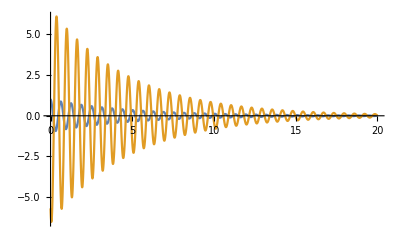

```mathematica
Signal =Exp[-τ Γ]*Cos[ω τ];

(*integral = Integrate[Signal,t]*)

analytical = (ⅇ^(-Γ (-Tw/2+t)) (-Γ Cos[(-Tw/2+t) ω]+ω Sin[(-Tw/2+t) ω]))/(Γ^2+ω^2)
ChosenGamma = 2*Pi*1/(30)
F
Plot[
{
Signal
/.Γ->ChosenGamma
/.ω->5,
F
/.Γ->ChosenGamma
/.ω->5
/. Tw -> 40
},
{τ,0,20},
PlotRange->Full
]
```

```mathematica
decayPoints = Table[{τ, Signal
/.Γ->ChosenGamma
/.ω->5},{τ, Range[0, 20, 0.01]}]
Export["decayPoints.txt",decayPoints,"Table"]

decayPoints = Table[{τ, 
F
/.Γ->ChosenGamma
/.ω->5
/. Tw -> 40
},{τ, Range[0, 20, 0.01]}]
Export["vnaDecayPoints.txt",decayPoints,"Table"]
```

{{0.,1.},{0.01,0.996661},{0.02,0.990845},{0.03,0.982578},{0.04,0.97189},{0.05,0.958819},{0.06,0.943406},{0.07,0.925701},{0.08,0.905757},{0.09,0.883633},{0.1,0.859394},{0.11,0.833108},{0.12,0.804851},{0.13,0.774701},1973,{19.87,0.00592212},{19.88,0.00662123},{19.89,0.00730088},{19.9,0.00795945},{19.91,0.00859538},{19.92,0.00920717},{19.93,0.0097934},{19.94,0.0103527},{19.95,0.0108838},{19.96,0.0113855},{19.97,0.0118567},{19.98,0.0122962},{19.99,0.0127032},{20.,0.0130767}}
 |  |  |  |

decayPoints.txt

{{0.,-6.19265},{0.01,-6.75199},{0.02,-7.29212},{0.03,-7.81177},{0.04,-8.30974},{0.05,-8.78485},{0.06,-9.23604},{0.07,-9.66225},{0.08,-10.0625},{0.09,-10.436},{0.1,-10.7819},{0.11,-11.0993},{0.12,-11.3877},{0.13,-11.6465},1974,{19.88,0.122631},{19.89,0.114035},{19.9,0.105191},{19.91,0.09612},{19.92,0.0868472},{19.93,0.0773961},{19.94,0.0677912},{19.95,0.058057},{19.96,0.0482184},{19.97,0.0383005},{19.98,0.0283284},{19.99,0.0183271},{20.,0.00832187}}
 |  |  |  |

vnaDecayPoints.txt

```mathematica
(ⅇ^(-t Γ) (-Γ Cos[ϕ+t ω]+ω Sin[t ω]))/(Γ^2+ω^2)

A = (ⅇ^(-t Γ) (-Γ Cos[t ω]+ω Sin[t ω]))/(Γ^2+ω^2)/.t->(τ+Tw/2)
B = (ⅇ^(-t Γ) (-Γ Cos[t ω]+ω Sin[t ω]))/(Γ^2+ω^2)/.t->(τ-Tw/2)
F = A-B
```

(ⅇ^(-t Γ) (-Γ Cos[ϕ+t ω]+ω Sin[t ω]))/(Γ^2+ω^2)

(ⅇ^(-Γ (Tw/2+τ)) (-Γ Cos[(Tw/2+τ) ω]+ω Sin[(Tw/2+τ) ω]))/(Γ^2+ω^2)

(ⅇ^(-Γ (-Tw/2+τ)) (-Γ Cos[(-Tw/2+τ) ω]+ω Sin[(-Tw/2+τ) ω]))/(Γ^2+ω^2)

-(ⅇ^(-Γ (-Tw/2+τ)) (-Γ Cos[(-Tw/2+τ) ω]+ω Sin[(-Tw/2+τ) ω]))/(Γ^2+ω^2)+(ⅇ^(-Γ (Tw/2+τ)) (-Γ Cos[(Tw/2+τ) ω]+ω Sin[(Tw/2+τ) ω]))/(Γ^2+ω^2)

1/(Γ^2+ω^2)ⅇ^(-2 Γ τ) (ⅇ^(Γ (Tw/2+τ)) Γ Cos[ϕ-(Tw ω)/2+τ ω]-ⅇ^(Γ (-Tw/2+τ)) Γ Cos[ϕ+(Tw/2+τ) ω]-ⅇ^(Γ (Tw/2+τ)) ω Sin[ϕ+(-Tw/2+τ) ω]+ⅇ^(Γ (-Tw/2+τ)) ω Sin[ϕ+(Tw/2+τ) ω])